```mathematica
urlCovid19="https://pomber.github.io/covid19/timeseries.json"
```

https://pomber.github.io/covid19/timeseries.json

```mathematica
cov19=Import[urlCovid19];
```

```mathematica
cov19[[1]]
```

Afghanistan→{{date→2020-1-22,confirmed→0,deaths→0,recovered→0},{date→2020-1-23,confirmed→0,deaths→0,recovered→0},826,{date→2022-4-29,confirmed→178873,deaths→7683,recovered→0},{date→2022-4-30,confirmed→178879,deaths→7683,recovered→0}}
 |  |  |  |

```mathematica
as19=Association[cov19]
```

<|Afghanistan→{{date→2020-1-22,confirmed→0,deaths→0,recovered→0},{date→2020-1-23,confirmed→0,deaths→0,recovered→0},826,{date→2022-4-29,confirmed→178873,deaths→7683,recovered→0},{date→2022-4-30,confirmed→178879,deaths→7683,recovered→0}},196,Zimbabwe→1|>
 |  |  |  |

```mathematica
asas19=Map[Association,as19,{3}]
```

<|Afghanistan→{{<|date→2020-1-22|>,<|confirmed→0|>,<|deaths→0|>,<|recovered→0|>},828,{<|date→2022-4-30|>,<|confirmed→178879|>,<|deaths→7683|>,<|recovered→0|>}},196,Zimbabwe→{{<|date→2020-1-22|>,<|confirmed→0|>,<|deaths→0|>,<|recovered→0|>},828,{1}}|>
 |  |  |  |

```mathematica
asas19["Japan"]
```

{{<|date→2020-1-22|>,<|confirmed→2|>,<|deaths→0|>,<|recovered→0|>},{<|date→2020-1-23|>,<|confirmed→2|>,<|deaths→0|>,<|recovered→0|>},826,{<|date→2022-4-29|>,<|confirmed→7846274|>,<|deaths→29553|>,<|recovered→0|>},{<|date→2022-4-30|>,<|confirmed→7871253|>,<|deaths→29567|>,<|recovered→0|>}}
 |  |  |  |

```mathematica
ts["Japan","confirmed"]=Map[{AbsoluteTime[#[[1]]["date"]],#[[2]]["confirmed"]}&,asas19["Japan"]]
```

{{3788640000,2},{3788726400,2},{3788812800,2},{3788899200,2},{3788985600,4},{3789072000,4},{3789158400,7},{3789244800,7},{3789331200,11},{3789417600,15},{3789504000,20},{3789590400,20},{3789676800,20},{3789763200,22},{3789849600,23},{3789936000,23},{3790022400,23},{3790108800,24},{3790195200,24},{3790281600,26},{3790368000,27},{3790454400,28},{3790540800,33},{3790627200,43},{3790713600,54},{3790800000,60},{3790886400,67},{3790972800,79},{3791059200,85},{3791145600,95},{3791232000,112},{3791318400,137},{3791404800,149},{3791491200,160},{3791577600,173},{3791664000,192},{3791750400,218},{3791836800,236},{3791923200,245},{3792009600,259},{3792096000,278},{3792182400,298},{3792268800,333},{3792355200,365},{3792441600,420},{3792528000,466},{3792614400,499},{3792700800,527},{3792787200,585},{3792873600,640},{3792960000,696},{3793046400,733},{3793132800,795},{3793219200,826},{3793305600,843},{3793392000,893},{3793478400,928},{3793564800,968},{3793651200,1022},{3793737600,1059},{3793824000,1104},{3793910400,1144},{3793996800,1217},{3794083200,1314},{3794169600,1416},{3794256000,1530},{3794342400,1728},{3794428800,1907},{3794515200,2001},{3794601600,2255},{3794688000,2535},{3794774400,2818},{3794860800,3154},{3794947200,3525},{3795033600,3876},{3795120000,4110},{3795206400,4485},{3795292800,5020},{3795379200,5614},{3795465600,6250},{3795552000,6951},{3795638400,7473},{3795724800,7773},{3795811200,8277},{3795897600,8835},{3795984000,9398},{3796070400,9958},{3796156800,10548},{3796243200,10914},{3796329600,11258},{3796416000,11641},{3796502400,12037},{3796588800,12469},{3796675200,12854},{3796761600,13186},{3796848000,13405},{3796934400,13576},{3797020800,13860},{3797107200,14076},{3797193600,14284},{3797280000,14558},{3797366400,14861},{3797452800,15061},{3797539200,15229},{3797625600,15354},{3797712000,15455},{3797798400,15553},{3797884800,15640},{3797971200,15755},{3798057600,15824},{3798144000,15861},{3798230400,15948},{3798316800,15998},{3798403200,16096},{3798489600,16148},{3798576000,16202},{3798662400,16226},{3798748800,16259},{3798835200,16287},{3798921600,16321},{3799008000,16362},{3799094400,16385},{3799180800,16410},{3799267200,16451},{3799353600,16472},{3799440000,16502},{3799526400,16528},{3799612800,16588},{3799699200,16661},{3799785600,16706},{3799872000,16741},{3799958400,16778},{3800044800,16829},{3800131200,16858},{3800217600,16902},{3800304000,16949},{3800390400,16995},{3800476800,17033},{3800563200,17054},{3800649600,17099},{3800736000,17135},{3800822400,17179},{3800908800,17240},{3800995200,17285},{3801081600,17360},{3801168000,17432},{3801254400,17474},{3801340800,17520},{3801427200,17589},{3801513600,17650},{3801600000,17714},{3801686400,17769},{3801772800,17812},{3801859200,17869},{3801945600,17965},{3802032000,18047},{3802118400,18152},{3802204800,18244},{3802291200,18357},{3802377600,18467},{3802464000,18605},{3802550400,18732},{3802636800,18926},{3802723200,19176},{3802809600,19450},{3802896000,19658},{3802982400,19834},{3803068800,20042},{3803155200,20249},{3803241600,20604},{3803328000,21034},{3803414400,21420},{3803500800,21827},{3803587200,22086},{3803673600,22419},{3803760000,22869},{3803846400,23493},{3803932800,24090},{3804019200,24751},{3804105600,25262},{3804192000,25680},{3804278400,26312},{3804364800,27107},{3804451200,28088},{3804537600,28867},{3804624000,29668},{3804710400,30507},{3804796800,31107},{3804883200,32092},{3804969600,33362},{3805056000,34670},{3805142400,36256},{3805228800,37790},{3805315200,39121},{3805401600,40086},{3805488000,41332},{3805574400,42687},{3805660800,44172},{3805747200,45777},{3805833600,47348},{3805920000,48789},{3806006400,49627},{3806092800,50324},{3806179200,51303},{3806265600,52475},{3806352000,53831},{3806438400,55062},{3806524800,56079},{3806611200,56726},{3806697600,57642},{3806784000,58712},{3806870400,59890},{3806956800,60927},{3807043200,61911},{3807129600,62655},{3807216000,63148},{3807302400,63863},{3807388800,64766},{3807475200,65629},{3807561600,66505},{3807648000,67349},{3807734400,67949},{3807820800,68385},{3807907200,69018},{3807993600,69610},{3808080000,70267},{3808166400,70854},{3808252800,71452},{3808339200,71903},{3808425600,72194},{3808512000,72703},{3808598400,73211},{3808684800,73923},{3808771200,74565},{3808857600,75211},{3808944000,75650},{3809030400,75916},{3809116800,76447},{3809203200,76998},{3809289600,77487},{3809376000,78059},{3809462400,78655},{3809548800,79135},{3809635200,79445},{3809721600,79776},{3809808000,79995},{3809894400,80477},{3809980800,81050},{3810067200,81689},{3810153600,82174},{3810240000,82476},{3810326400,83003},{3810412800,83579},{3810499200,84212},{3810585600,84754},{3810672000,85328},{3810758400,85728},{3810844800,86007},{3810931200,86507},{3811017600,87013},{3811104000,87640},{3811190400,88243},{3811276800,88921},{3811363200,89357},{3811449600,89635},{3811536000,90133},{3811622400,90685},{3811708800,91393},{3811795200,92032},{3811881600,92655},{3811968000,93085},{3812054400,93401},{3812140800,93882},{3812227200,94497},{3812313600,95113},{3812400000,95858},{3812486400,96584},{3812572800,97077},{3812659200,97487},{3812745600,98133},{3812832000,98864},{3812918400,99672},{3813004800,100446},{3813091200,101323},{3813177600,101936},{3813264000,102423},{3813350400,103288},{3813436800,103912},{3813523200,104960},{3813609600,106103},{3813696000,107436},{3813782400,108386},{3813868800,109166},{3813955200,110449},{3814041600,111993},{3814128000,113652},{3814214400,115356},{3814300800,117091},{3814387200,118530},{3814473600,119480},{3814560000,121180},{3814646400,123374},{3814732800,125759},{3814819200,128180},{3814905600,130772},{3814992000,132931},{3815078400,134449},{3815164800,135678},{3815251200,137620},{3815337600,140120},{3815424000,142651},{3815510400,145326},{3815596800,147388},{3815683200,148824},{3815769600,150857},{3815856000,153289},{3815942400,155806},{3816028800,158258},{3816115200,160766},{3816201600,162804},{3816288000,164335},{3816374400,166511},{3816460800,169321},{3816547200,172290},{3816633600,175085},{3816720000,178122},{3816806400,180505},{3816892800,182186},{3816979200,184612},{3817065600,187608},{3817152000,190817},{3817238400,193654},{3817324800,196643},{3817411200,199134},{3817497600,200945},{3817584000,203639},{3817670400,206915},{3817756800,210661},{3817843200,214493},{3817929600,218378},{3818016000,221322},{3818102400,223719},{3818188800,227346},{3818275200,231217},{3818361600,235749},{3818448000,239005},{3818534400,242076},{3818620800,245242},{3818707200,248585},{3818793600,253534},{3818880000,259583},{3818966400,267225},{3819052800,275182},{3819139200,283036},{3819225600,289144},{3819312000,294050},{3819398400,298647},{3819484800,304564},{3819571200,311220},{3819657600,318393},{3819744000,325435},{3819830400,331195},{3819916800,336132},{3820003200,341467},{3820089600,347029},{3820176000,352693},{3820262400,357750},{3820348800,362476},{3820435200,366466},{3820521600,369229},{3820608000,373082},{3820694400,377056},{3820780800,381187},{3820867200,384725},{3820953600,388067},{3821040000,390740},{3821126400,392533},{3821212800,394857},{3821299200,397491},{3821385600,400069},{3821472000,402439},{3821558400,404716},{3821644800,406346},{3821731200,407563},{3821817600,409131},{3821904000,411017},{3821990400,412707},{3822076800,414007},{3822163200,415367},{3822249600,416729},{3822336000,417694},{3822422400,419002},{3822508800,420450},{3822595200,421986},{3822681600,423287},{3822768000,424520},{3822854400,425552},{3822940800,426292},{3823027200,427373},{3823113600,428294},{3823200000,429370},{3823286400,430424},{3823372800,431637},{3823459200,432636},{3823545600,433334},{3823632000,434222},{3823718400,435465},{3823804800,436634},{3823891200,437782},{3823977600,438825},{3824064000,439896},{3824150400,440496},{3824236800,441623},{3824323200,442936},{3824409600,444253},{3824496000,445524},{3824582400,446843},{3824668800,447830},{3824755200,448525},{3824841600,449658},{3824928000,451191},{3825014400,452688},{3825100800,454151},{3825187200,455667},{3825273600,456785},{3825360000,457601},{3825446400,459101},{3825532800,461018},{3825619200,462933},{3825705600,464958},{3825792000,467029},{3825878400,468811},{3825964800,470156},{3826051200,472243},{3826137600,475086},{3826224000,477691},{3826310400,480445},{3826396800,483217},{3826483200,485684},{3826569600,487255},{3826656000,489921},{3826742400,493369},{3826828800,496865},{3826915200,500353},{3827001600,504118},{3827088000,506954},{3827174400,509058},{3827260800,512510},{3827347200,516817},{3827433600,521386},{3827520000,525910},{3827606400,530703},{3827692800,534787},{3827779200,537690},{3827865600,542040},{3827952000,547326},{3828038400,552818},{3828124800,557922},{3828211200,563517},{3828297600,568116},{3828384000,571430},{3828470400,576391},{3828556800,582174},{3828643200,588087},{3828729600,592771},{3828816000,598754},{3828902400,604644},{3828988800,609108},{3829075200,613298},{3829161600,617358},{3829248000,621728},{3829334400,627778},{3829420800,635016},{3829507200,641500},{3829593600,646440},{3829680000,652675},{3829766400,659726},{3829852800,666600},{3829939200,672862},{3830025600,679279},{3830112000,684535},{3830198400,688212},{3830284800,693436},{3830371200,699227},{3830457600,704939},{3830544000,710184},{3830630400,715219},{3830716800,719258},{3830803200,721969},{3830889600,725861},{3830976000,730394},{3831062400,734526},{3831148800,738229},{3831235200,741822},{3831321600,744696},{3831408000,746487},{3831494400,749126},{3831580800,752160},{3831667200,754991},{3831753600,757583},{3831840000,760233},{3831926400,762253},{3832012800,763533},{3832099200,765414},{3832185600,767652},{3832272000,769694},{3832358400,771628},{3832444800,773569},{3832531200,774951},{3832617600,775884},{3832704000,777301},{3832790400,779008},{3832876800,780558},{3832963200,782178},{3833049600,783696},{3833136000,785002},{3833222400,785870},{3833308800,787305},{3833395200,789085},{3833481600,790759},{3833568000,792469},{3833654400,794100},{3833740800,795382},{3833827200,796383},{3833913600,797763},{3834000000,799583},{3834086400,801337},{3834172800,803112},{3834259200,804990},{3834345600,806475},{3834432000,807504},{3834518400,809172},{3834604800,811361},{3834691200,813607},{3834777600,815883},{3834864000,818341},{3834950400,820371},{3835036800,821876},{3835123200,824260},{3835209600,827452},{3835296000,830870},{3835382400,834303},{3835468800,838189},{3835555200,841290},{3835641600,843618},{3835728000,847377},{3835814400,852326},{3835900800,857725},{3835987200,861959},{3836073600,865553},{3836160000,870592},{3836246400,875301},{3836332800,882971},{3836419200,892599},{3836505600,903351},{3836592000,914182},{3836678400,926604},{3836764800,936852},{3836851200,945330},{3836937600,957431},{3837024000,971743},{3837110400,987060},{3837196800,1002867},{3837283200,1018688},{3837369600,1033214},{3837456000,1045392},{3837542400,1056125},{3837628800,1072153},{3837715200,1091187},{3837801600,1111683},{3837888000,1131986},{3837974400,1149874},{3838060800,1164881},{3838147200,1184986},{3838233600,1209082},{3838320000,1234423},{3838406400,1260415},{3838492800,1286077},{3838579200,1308422},{3838665600,1325346},{3838752000,1347015},{3838838400,1371426},{3838924800,1396464},{3839011200,1420783},{3839097600,1443642},{3839184000,1462979},{3839270400,1476653},{3839356800,1494372},{3839443200,1514400},{3839529600,1532616},{3839616000,1549337},{3839702400,1565351},{3839788800,1578258},{3839875200,1586482},{3839961600,1597089},{3840048000,1609477},{3840134400,1619873},{3840220800,1628732},{3840307200,1637534},{3840393600,1644747},{3840480000,1648920},{3840566400,1655199},{3840652800,1662008},{3840739200,1667699},{3840825600,1672812},{3840912000,1677512},{3840998400,1680908},{3841084800,1683129},{3841171200,1684899},{3841257600,1688142},{3841344000,1691743},{3841430400,1693838},{3841516800,1696508},{3841603200,1698644},{3841689600,1699792},{3841776000,1701514},{3841862400,1703497},{3841948800,1705072},{3842035200,1706516},{3842121600,1707759},{3842208000,1708726},{3842294400,1709325},{3842380800,1710304},{3842467200,1711429},{3842553600,1712401},{3842640000,1713228},{3842726400,1714002},{3842812800,1714555},{3842899200,1714924},{3842985600,1715531},{3843072000,1716262},{3843158400,1716879},{3843244800,1717396},{3843331200,1717896},{3843417600,1718324},{3843504000,1718554},{3843590400,1718925},{3843676800,1719313},{3843763200,1719656},{3843849600,1719980},{3843936000,1720263},{3844022400,1720495},{3844108800,1720646},{3844195200,1720956},{3844281600,1721266},{3844368000,1721539},{3844454400,1721831},{3844540800,1722115},{3844627200,1722343},{3844713600,1722427},{3844800000,1722648},{3844886400,1722912},{3844972800,1723070},{3845059200,1723295},{3845145600,1723525},{3845232000,1723682},{3845318400,1723782},{3845404800,1723976},{3845491200,1724172},{3845577600,1724379},{3845664000,1724573},{3845750400,1724767},{3845836800,1724893},{3845923200,1724967},{3846009600,1725111},{3846096000,1725310},{3846182400,1725458},{3846268800,1725611},{3846355200,1725715},{3846441600,1725850},{3846528000,1725894},{3846614400,1726001},{3846700800,1726074},{3846787200,1726186},{3846873600,1726299},{3846960000,1726419},{3847046400,1726479},{3847132800,1726555},{3847219200,1726636},{3847305600,1726751},{3847392000,1726864},{3847478400,1727005},{3847564800,1727125},{3847651200,1727229},{3847737600,1727283},{3847824000,1727382},{3847910400,1727504},{3847996800,1727658},{3848083200,1727794},{3848169600,1727925},{3848256000,1728023},{3848342400,1728090},{3848428800,1728218},{3848515200,1728377},{3848601600,1728540},{3848688000,1728701},{3848774400,1728880},{3848860800,1729030},{3848947200,1729139},{3849033600,1729357},{3849120000,1729577},{3849206400,1729824},{3849292800,1730084},{3849379200,1730347},{3849465600,1730572},{3849552000,1730735},{3849638400,1731048},{3849724800,1731446},{3849811200,1731878},{3849897600,1732296},{3849984000,1732752},{3850070400,1733229},{3850156800,1733901},{3850243200,1735050},{3850329600,1737540},{3850416000,1741837},{3850502400,1747907},{3850588800,1756209},{3850675200,1764280},{3850761600,1770545},{3850848000,1776780},{3850934400,1789824},{3851020800,1808501},{3851107200,1830381},{3851193600,1856002},{3851280000,1881481},{3851366400,1902304},{3851452800,1934391},{3851539200,1975761},{3851625600,2021758},{3851712000,2071471},{3851798400,2125882},{3851884800,2175719},{3851971200,2220382},{3852057600,2282871},{3852144000,2354358},{3852230400,2433094},{3852316800,2514804},{3852403200,2599599},{3852489600,2677602},{3852576000,2738460},{3852662400,2820053},{3852748800,2914824},{3852835200,3019169},{3852921600,3117346},{3853008000,3219621},{3853094400,3309439},{3853180800,3377378},{3853267200,3478462},{3853353600,3576261},{3853440000,3675865},{3853526400,3774164},{3853612800,3842551},{3853699200,3919931},{3853785600,3979984},{3853872000,4064142},{3853958400,4155027},{3854044800,4250142},{3854131200,4337780},{3854217600,4419254},{3854304000,4490748},{3854390400,4542657},{3854476800,4612104},{3854563200,4692406},{3854649600,4753558},{3854736000,4819151},{3854822400,4891242},{3854908800,4954865},{3854995200,5005881},{3855081600,5071249},{3855168000,5143818},{3855254400,5214086},{3855340800,5277655},{3855427200,5341246},{3855513600,5395143},{3855600000,5432145},{3855686400,5486083},{3855772800,5549755},{3855859200,5610818},{3855945600,5666630},{3856032000,5721856},{3856118400,5772715},{3856204800,5805074},{3856291200,5855769},{3856377600,5913591},{3856464000,5967069},{3856550400,6016178},{3856636800,6060771},{3856723200,6100331},{3856809600,6127897},{3856896000,6148049},{3856982400,6188977},{3857068800,6238527},{3857155200,6285894},{3857241600,6333118},{3857328000,6376338},{3857414400,6406058},{3857500800,6450423},{3857587200,6504032},{3857673600,6555585},{3857760000,6604726},{3857846400,6653421},{3857932800,6700637},{3858019200,6730654},{3858105600,6776236},{3858192000,6830997},{3858278400,6885876},{3858364800,6937720},{3858451200,6990349},{3858537600,7039397},{3858624000,7072493},{3858710400,7122173},{3858796800,7179839},{3858883200,7235040},{3858969600,7284737},{3859056000,7332261},{3859142400,7371466},{3859228800,7395608},{3859315200,7436434},{3859401600,7484263},{3859488000,7531317},{3859574400,7574215},{3859660800,7618107},{3859747200,7656600},{3859833600,7681363},{3859920000,7721795},{3860006400,7767997},{3860092800,7809668},{3860179200,7846274},{3860265600,7871253}}

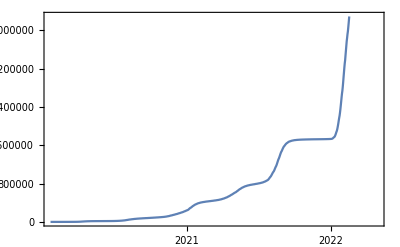

```mathematica
DateListPlot[ts["Japan","confirmed"]]
```

```mathematica
its["Japan","confirmed"]=Interpolation[ts["Japan","confirmed"]]
```

InterpolatingFunction[…]

```mathematica
startTime["Japan"]=AbsoluteTime[asas19["Japan"][[1]][[1]]["date"]]
```

3788640000

```mathematica
endTime["Japan"]=AbsoluteTime[asas19["Japan"][[-1]][[1]]["date"]]
```

3860265600

```mathematica
days["Japan"]=(endTime["Japan"]-startTime["Japan"])/60/60/24
```

829

```mathematica
count["Japan","confirmed"]=Table[its["Japan","confirmed"][t],{t,startTime["Japan"],endTime["Japan"],60*60*24}];
```

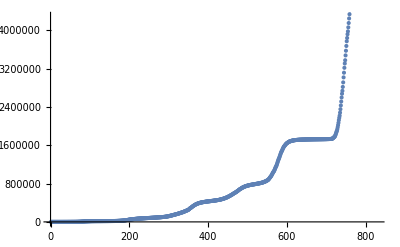

```mathematica
ListPlot[count["Japan","confirmed"]]
```

```mathematica
fou["Japan","confirmed"]=Fourier[count["Japan","confirmed"]];
```

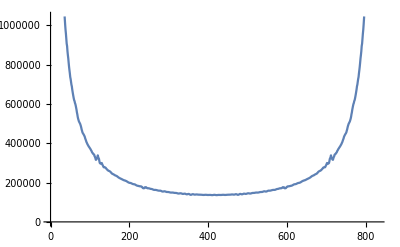

```mathematica
ListLinePlot[fou["Japan","confirmed"]//Abs]
```